Mathematical Techniques in Evolution and Ecology

# Some classic models in evolution and ecology

Based on chapter 3 in Otto and Day (2007)

Spring Quarter 2015
Simon Aeschbacher
saeschbacher@ucdavis.edu

## Outline

### Goals

To introduce/revisit some classic models in evolution and ecology

To derive dynamical equations, some of which will be analysed in later units

### Concepts

Exponential growth

Logistic growth

Linear and non-linear models

Symmetric models

Normalisation

Competition models

Not discussed, but in the book:

Consumer–resource models (e.g. predator–prey models)

SIR epidemiological models

## Exponential and logistic models of population growth

Common assumptions:

Constant environment

No interaction with other species (no competition, predation etc.)

Specific assumptions:

Exponential growth: constant amount of resources

Logistic growth: amount of resources decreases with increasing population size

### Exponential population growth

Assumes that the variable changes at a rate proportional to its current value.

All individuals reproduce (we can choose to model only the females)

Do not keep track of age → can account for nonoverlapping and overlapping generations

Variable: n(t) for the # of indiv. at time t

Parameters: b, per capita # of births (continuous time: birth rate); d, fraction of population dying (death rate)

Life-cycle and flow diagram:

#### Discrete-time version

Recursion equation (from the life-cycle diagram):

n (t+1)=(1-b) (1-d) n t

Note that, here, it does not matter whether births or deaths happen first. But recall the squirrel example!

Define the compound parameter R=(1-d)(1+b) as the number of surviving individuals per parent, or the reproductive factor. Hence

n (t+1)=n R t

Difference equation:

Δn=n (t+1)-n t=n (R-1) t

Define the discrete-time growth rate (per capita change in # of individuals) as r_d=R-1=b-d-b d.

#### Continuous-time version

Now, b and d denote the per capita rate of growth and death, respectively. Multiplied by a small amount of time Δt, they give the # of births and deaths per individual in this time interval.

Differential equation (from the flow diagram):

(ⅆ n)/ⅆt=b n(t)-d n(t)=r_c n(t),

where r_c=b-d is the per capita rate of change in the # of individuals.

### Logistic population growth

Many factors may slow the rate of growth, e.g. declining resource availability, increased predation risk, higher incidence of disease, etc. The logistic model describes this processes indirectly, and there are many ways of modeling the effect.

#### Discrete-time version

The standard logistic model in discrete time assumes that the number of surviving individuals per parent declines linearly with population size. That is, the reproductive factor is modelled as

R(n)=intercept+slope * n(t) =(1+r_d)+(-r_d/K)n(t),

where K is the carrying capacity. The population grows, i.e. R(n)>1, if n(t)<K, and shrinks, i.e. R(n)<1, if n(t)>K. No change occurs if n(t)=K.

```mathematica
logGrowthReproFactorPlot
```

Recursion equation:

n(t+1)=R(n) n(t)=[(1+r_d)-r_d/K n(t)]n(t)=n(t)+r_d n(t)(1-(n(t))/K).

Difference equation:

Δn=n(t+1)-n(t)=r_d n(t)(1-(n(t))/K).

#### Continuous-time version

We leave the derivation of the differential equation as homework (Problem 2).

#### Illustration: Discrete-time version of logistic growth model

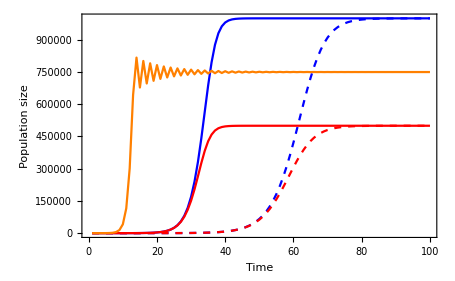

```mathematica
plotLogGrowth[(* K: *){10^6,10^6,5 10^5,5 10^5,7.5 10^5},(* r: *){0.5,0.25,0.5,0.25,1.9},(* tMax: *){100,100,100,100,100},(* Style: *){{Blue},{Blue,Dashed},{Red},{Red,Dashed},{Orange}}]
```

Notice the cyclic behaviour, eventually converging to K=750000, of the orange line, which occurs if r_d is above a critical value.

## Linear and nonlinear models

Linear models: The change per unit time is a linear function of the variable(s)

Example: Exponential growth model, Δn=(R-1) n(t)=r_d n(t).

Nonlinear models: The change per unit time is a ‘more complicated’, non-linear function of the variable(s)

Example: Logistic growth model, Δn=r_d n(t)(1-(n(t))/K)=r_d n(t)-r_d(n(t))^2/K.

It is straightforward to obtain the general solution of linear models, i.e. there is an explicit solution predicting what the value of the variable will be at any future point in time (See unit 6 / chapter 6).

However, for non-linear models, this can be difficult or even impossible. In biology, most models are non-linear, as they often involve interactions.

Remark: Recursion, difference, and differential equations are implicit descriptions.

## Haploid and diploid models of natural selection

We will study two basic, but very important deterministic population-genetic models. Population-genetic models describe how the frequency of alleles changes over time. We consider one locus with two alleles called A and a, where one allele is favoured over the other by natural selection.
Sexual organisms go through a haploid and a diploid phase in their life cycle. Whether the haploid or diploid model of selection is appropriate depends on when selection acts:

### Haploid model of selection

## Problem assignment

We constructed the differential equation for the continuous-time version of the exponential growth model from the flow diagram. (a) Instead, derive the equation from the difference equation of the discrete-time version. Hint: introduce a small amount of time Δt and take the appropriate limit. (b) Comparing r_d and r_c, explain the difference between the discrete- and continuous-time versions.

Derive the differential equation for the logistic growth model in continuous time. Start by assuming that the per capita growth rate r(n) declines linearly with population size n(t). Assume that r(n) has a maximum equal to the intrinsic growth rate r_c when there are no competitors (i.e. r(0)=r_c), and that it reaches zero when the population is at the carrying capacity (i.e. r(K)=0). Substitute r(n) for r_c in the differential equation of the exponential growth model to obtain the result of interest.

As an alternative way of deriving the continuous-time version of the haploid selection model, start from the continous-time version of the exponential growth model. Specifically, let n_A and n_a be the number of individuals carrying alleles A and a, respectively, and let the growth rate depend on the allelic state, i.e. r_A=(b_A-d_A) for carriers of A, and r_a=(b_a-d_a) for carriers of a. From the exponential growth model, we have (ⅆ n_A)/ⅆt=r_A n_A(t) and (ⅆ n_a)/ⅆt=r_a n_a(t). But we want to know how the allele frequencies change! As these sum to 1, it is sufficient to follow only the frequency of allele A, p(t)=n_A(t)/[n_A(t)+n_a(t)] . Start by writing

(ⅆp(t))/ⅆt=ⅆ[(n_A(t))/(n_A(t)+n_a(t))]/ⅆt,

then use the quotient rule to evaluate the derivative, and use the equations for (ⅆ n_A)/ⅆt and (ⅆ n_a)/ⅆt to express ⅆp/ⅆt in terms of r_A, r_a, and p.

## Handouts

Box 2.3: Seven steps to modelling a biological problem

Box 2.6: The relationship between discrete-time and continuous-time models

Copy of Appendix 2

## Initialisation cells

```mathematica
logGrowthReproFactor[n_,rd_,K_]:=(1+rd)-rd/K n
```

```mathematica
logGrowthReproFactorPlot:=Manipulate[
Plot[logGrowthReproFactor[n,rd,K],{n,0,2K},
PlotRange->{{0,2K},{0,1.05(1+rd)}},
Frame->True,
FrameLabel->{{"Reproductive factor, R(n)",""},{"Population size, n(t)","K = "<>ToString[ Round[K]]<>"; r_d = "<>ToString[Round[rd,0.01]]}},
LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14],
GridLines->{{K},{1}}],
{{rd,1},0,2},{{K,100},10,200}
]
```

```mathematica
Clear[n]
n[0,KK_,r_]:=n[0,KK,r]=1;
n[t_,KK_,r_]:=n[t,KK,r]=N[n[t-1,KK,r]+r n[t-1,KK,r](1-n[t-1,KK,r]/KK)]
```

```mathematica
plotDataListLogGrowth[KK_,r_,tMax_]:=Table[n[t,KK,r]//N,{t,1,tMax}]
```

```mathematica
plotLogGrowth[KList_,rList_,tMaxList_,styleList_]:=
ListLinePlot[MapThread[plotDataListLogGrowth[#1,#2,#3]&,{KList,rList,tMaxList}],
Frame->True,
FrameLabel->{"Time","Population size"},
LabelStyle->{FontFamily->"Helvetica",FontSize->14},
PlotStyle->styleList
]
```